```mathematica
Quit[];
```

```mathematica
(*units*)
ns=1*10^-9;
us=1*10^-6;
MHz=1*10^6;
ps=1*10^-12;
```

```mathematica
(*1st March tests*)
DataPico4thMarch=Import["G:\\Shared drives\\Ions\\03 - Projects\\Current Projects\\Rb Ba+ hybrid\\493 Photon Shape Tests\\4th Mar tests_1.dat",HeaderLines->10];
NData493p1=Flatten[DataPico4thMarch[[All,1]]];(*650 nm AOM pulsed at 200 ns - 5 uW*)
NData493p2=Flatten[DataPico4thMarch[[All,2]]];(*650 nm AOM pulsed at 200 ns - 5 uW background*)
NData493p3=Flatten[DataPico4thMarch[[All,3]]];(*650 nm AOM pulsed at 200 ns - 5 uW*)
NData493p4=Flatten[DataPico4thMarch[[All,4]]];(*650 nm AOM pulsed at 200 ns - 5 uW background*)
(*NData780p1=Flatten[DataPico1stMarch1[[All,5]]];(*650 nm AOM pulsed at 200 ns - 5.5 uW*)
NData780p2=Flatten[DataPico1stMarch1[[All,6]]];(*650 nm AOM pulsed at 200 ns - 5.5 uW*)*)
```

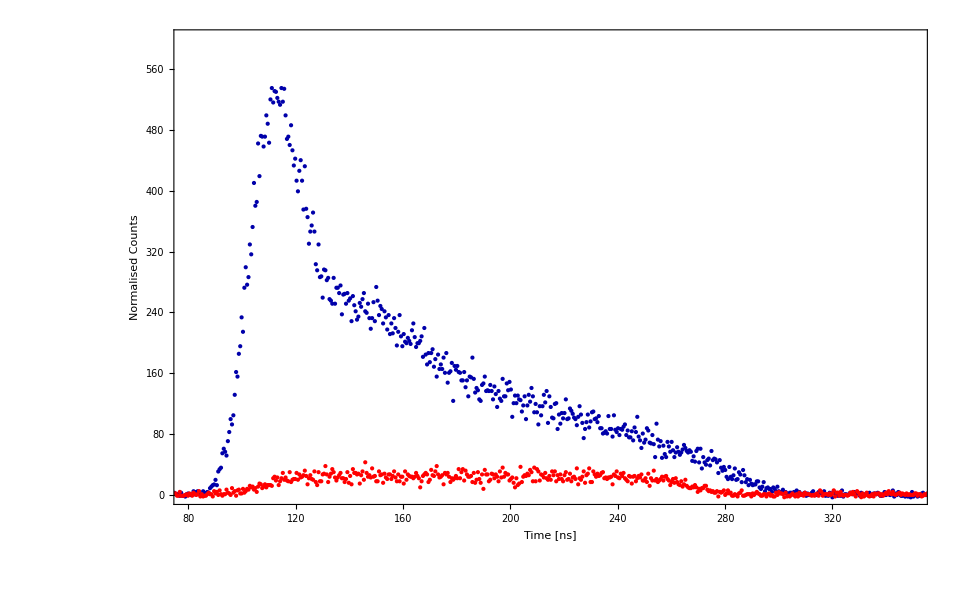

```mathematica
PicoBins=1;
BigBins493p1=Flatten[w={};Do[w={w,Total[NData493p1[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
BigBins493p2=Flatten[w={};Do[w={w,Total[NData493p2[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
BigBins493p3=Flatten[w={};Do[w={w,Total[NData493p3[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
BigBins493p4=Flatten[w={};Do[w={w,Total[NData493p4[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
TimeRange493=Range[(0)ns,(3583.6-0) ns,(512 ps*PicoBins)];
DataPhoton1=BigBins493p1-BigBins493p2;
DataPhoton2=BigBins493p3-BigBins493p4;
(*BigBins780p1=Flatten[w={};Do[w={w,Total[NData780p1[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
BigBins780p2=Flatten[w={};Do[w={w,Total[NData780p2[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
TimeRange780=Range[(0)ns,(3583.6-0) ns,(512 ps*PicoBins)];
DataPhoton1780=BigBins780p1;
DataPhoton2780=BigBins780p2;*)
(*DataPHOTON780p1=Transpose[{TimeRange780/ns,(BigBins780p1-Mean[Take[(BigBins780p1),{1,100}]])}];
DataPHOTON780p2=Transpose[{TimeRange780/ns,(BigBins780p2-Mean[Take[(BigBins780p2),{1,100}]])}];*)
DataPHOTON493p1=Transpose[{TimeRange493/ns,(BigBins493p1-Mean[Take[(BigBins493p1),{1,100}]])}];
DataPHOTON493p2=Transpose[{TimeRange493/ns,(BigBins493p2-Mean[Take[(BigBins493p2),{1,100}]])}];
(*DataPhoton1493=Transpose[{TimeRange493/ns,(DataPhoton1-Mean[Take[(DataPhoton1),{1,100}]])}];
DataPHOTON493p3=Transpose[{TimeRange493/ns,(BigBins493p3-Mean[Take[(BigBins493p3),{1,100}]])}];
DataPHOTON493p4=Transpose[{TimeRange493/ns,(BigBins493p4-Mean[Take[(BigBins493p4),{1,100}]])}];
DataPhoton2493=Transpose[{TimeRange493/ns,(DataPhoton2-Mean[Take[(DataPhoton2),{1,100}]])}];*)
PicoBins=1;
DataPlot=ListPlot[{DataPHOTON493p1,DataPHOTON493p2},Axes->False,Frame->True,FrameLabel->{"Time [ns]","Normalised Counts"},Joined->False,PlotStyle->{{PointSize[Large],Darker[Blue]},{PointSize[Large],Red},{PointSize[Large],Green},{PointSize[Large],Lighter[Blue]},{PointSize[Large],Brown}},PlotRange->{{80,350},{-1,600}},FrameStyle->Directive[Thick,Black,40]]
```

```mathematica
CountsBkgSub=(DataPhoton2-Mean[Take[(DataPhoton2),{1,100}]]);
PhotonCounts=N[Total[Take[CountsBkgSub,{156,684}]]]
TotalReps=4*10^5*120;
PhotonProb=(PhotonCounts/TotalReps)*10^3
```

64520.8

1.34418

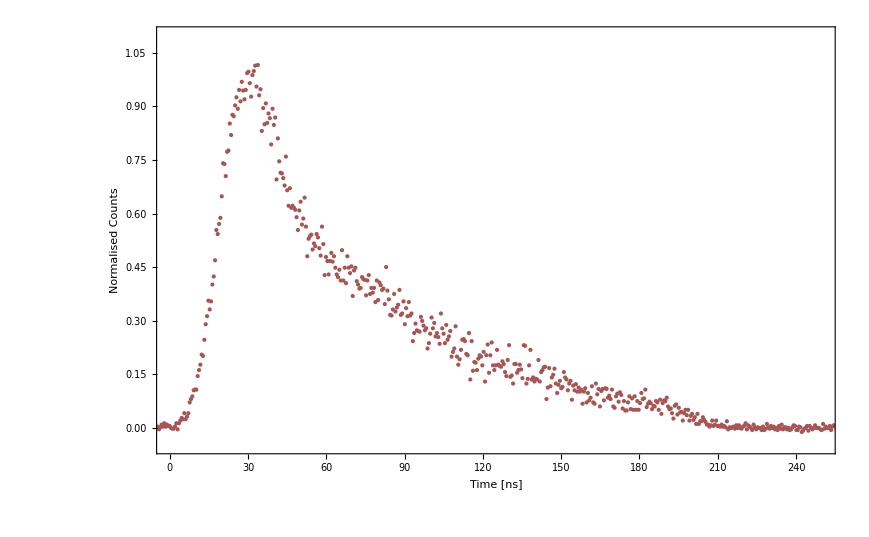

```mathematica
TimeRange493A=Range[(-85)ns,(3583.6-85) ns,(512 ps*PicoBins)];
DataPhoton2=(BigBins493p3-BigBins493p4)/530;
DataPhoton1493=Transpose[{TimeRange493A/ns,(DataPhoton2-Mean[Take[(DataPhoton2),{1,100}]])}];
DataPlot1=ListPlot[{DataPhoton1493},Axes->False,Frame->True,FrameLabel->{"Time [ns]","Normalised Counts"},Joined->False,PlotStyle->{{PointSize[Large],Darker[Pink]},{PointSize[Large],Red},{PointSize[Large],Green},{PointSize[Large],Lighter[Blue]},{PointSize[Large],Brown}},PlotRange->{{0,250},{-0.05,1.1}},FrameStyle->Directive[Thick,Black,40]]
```

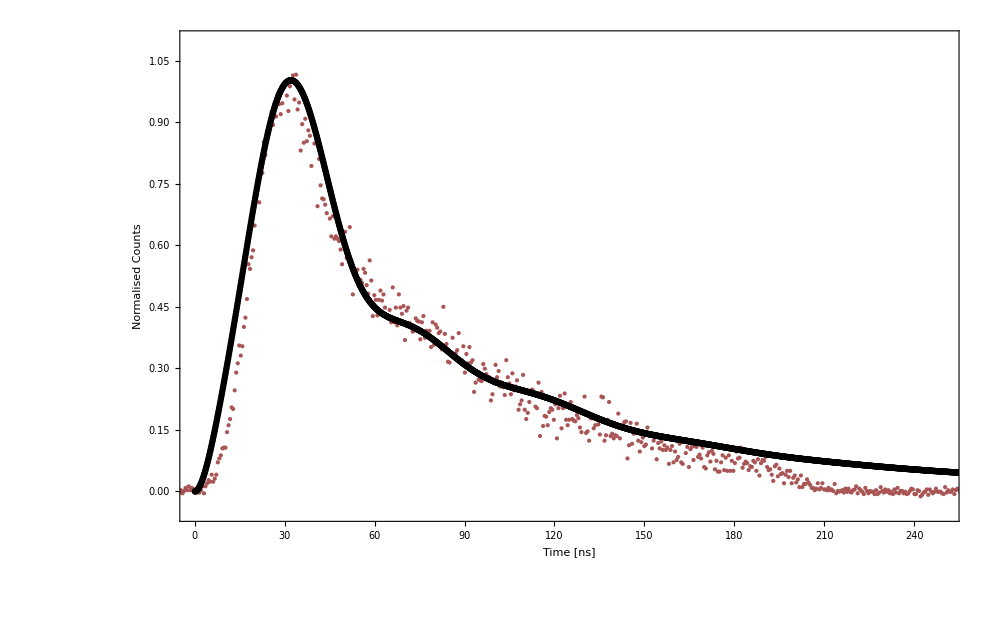

```mathematica
QutipData=Import["G:\\Shared drives\\Ions\\03 - Projects\\Current Projects\\Rb Ba+ hybrid\\493 Photon Shape Tests\\493PhotonShape_Orp0_Orsp15_Orm15.dat"];
PhotonTheory=Flatten[QutipData[[All,1]]];
PhotonTheoryPlot=ListPlot[PhotonTheory/0.14,DataRange->{0,300},PlotRange->All,PlotStyle->Black];
Show[DataPlot1,PhotonTheoryPlot]
```

```mathematica
(*12th March tests*)
DataPico12thMarch=Import["G:\\Shared drives\\Ions\\03 - Projects\\Current Projects\\Rb Ba+ hybrid\\493 Photon Shape Tests\\12th Mar tests_1.dat",HeaderLines->10];
NData493p1=Flatten[DataPico12thMarch[[All,4]]];(*650 nm AOM pulsed at 200 ns - 5 uW*)
NData493p2=Flatten[DataPico12thMarch[[All,5]]];(*650 nm AOM pulsed at 200 ns - 5 uW background*)
NData493p3=Flatten[DataPico12thMarch[[All,6]]];(*650 nm AOM pulsed at 200 ns - 5 uW*)
NData493p4=Flatten[DataPico12thMarch[[All,7]]];(*650 nm AOM pulsed at 200 ns - 5 uW background*)
```

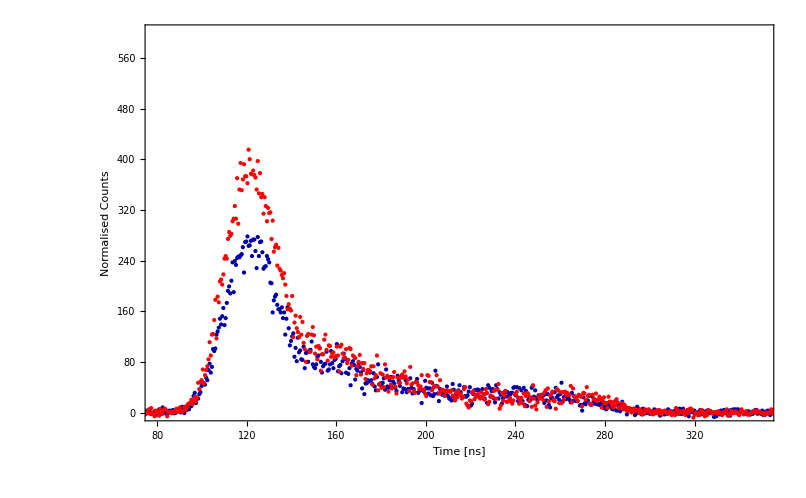

```mathematica
PicoBins=1;
BigBins493p1=Flatten[w={};Do[w={w,Total[NData493p1[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
BigBins493p2=Flatten[w={};Do[w={w,Total[NData493p2[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
BigBins493p3=Flatten[w={};Do[w={w,Total[NData493p3[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
BigBins493p4=Flatten[w={};Do[w={w,Total[NData493p4[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
TimeRange493=Range[(0)ns,(3583.6-0) ns,(512 ps*PicoBins)];
DataPhoton1=BigBins493p1-BigBins493p2;
DataPhoton2=BigBins493p3-BigBins493p4;
(*BigBins780p1=Flatten[w={};Do[w={w,Total[NData780p1[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
BigBins780p2=Flatten[w={};Do[w={w,Total[NData780p2[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
TimeRange780=Range[(0)ns,(3583.6-0) ns,(512 ps*PicoBins)];
DataPhoton1780=BigBins780p1;
DataPhoton2780=BigBins780p2;*)
(*DataPHOTON780p1=Transpose[{TimeRange780/ns,(BigBins780p1-Mean[Take[(BigBins780p1),{1,100}]])}];
DataPHOTON780p2=Transpose[{TimeRange780/ns,(BigBins780p2-Mean[Take[(BigBins780p2),{1,100}]])}];*)
DataPHOTON493p1=Transpose[{TimeRange493/ns,(DataPhoton1-Mean[Take[(DataPhoton1),{1,100}]])}];
DataPHOTON493p2=Transpose[{TimeRange493/ns,(DataPhoton2-Mean[Take[(DataPhoton2),{1,100}]])}];
(*DataPhoton1493=Transpose[{TimeRange493/ns,(DataPhoton1-Mean[Take[(DataPhoton1),{1,100}]])}];
DataPHOTON493p3=Transpose[{TimeRange493/ns,(BigBins493p3-Mean[Take[(BigBins493p3),{1,100}]])}];
DataPHOTON493p4=Transpose[{TimeRange493/ns,(BigBins493p4-Mean[Take[(BigBins493p4),{1,100}]])}];
DataPhoton2493=Transpose[{TimeRange493/ns,(DataPhoton2-Mean[Take[(DataPhoton2),{1,100}]])}];*)
PicoBins=1;
DataPlot=ListPlot[{DataPHOTON493p1,DataPHOTON493p2},Axes->False,Frame->True,FrameLabel->{"Time [ns]","Normalised Counts"},Joined->False,PlotStyle->{{PointSize[Large],Darker[Blue]},{PointSize[Large],Red},{PointSize[Large],Green},{PointSize[Large],Lighter[Blue]},{PointSize[Large],Brown}},PlotRange->{{80,350},{-1,600}},FrameStyle->Directive[Thick,Black,40]]
```

```mathematica
CountsBkgSub=(DataPhoton2-Mean[Take[(DataPhoton2),{1,100}]]);
PhotonCounts=N[Total[Take[CountsBkgSub,{156,684}]]]
TotalReps=4*10^5*120;
PhotonProb=(PhotonCounts/TotalReps)*10^3
```

34335.

0.715313

```mathematica
(*12th March tests*)
DataPico12thMarch=Import["G:\\Shared drives\\Ions\\03 - Projects\\Current Projects\\Rb Ba+ hybrid\\493 Photon Shape Tests\\12 Mar tests_2.dat",HeaderLines->10];
NData493p1=Flatten[DataPico12thMarch[[All,3]]];(*650 nm AOM pulsed at 200 ns - 5 uW*)
NData493p2=Flatten[DataPico12thMarch[[All,4]]];(*650 nm AOM pulsed at 200 ns - 5 uW background*)
```

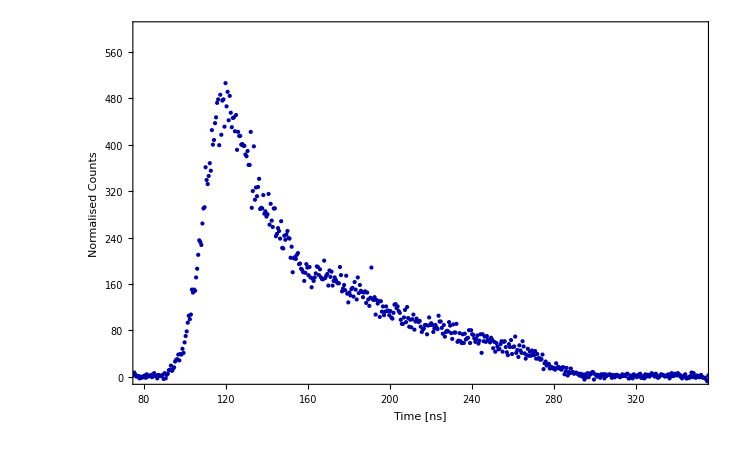

```mathematica
PicoBins=1;
BigBins493p1=Flatten[w={};Do[w={w,Total[NData493p1[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
BigBins493p2=Flatten[w={};Do[w={w,Total[NData493p2[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
TimeRange493=Range[(0)ns,(3583.6-0) ns,(512 ps*PicoBins)];
DataPhoton1=BigBins493p1-BigBins493p2;
DataPHOTON493p1=Transpose[{TimeRange493/ns,(DataPhoton1-Mean[Take[(DataPhoton1),{1,100}]])}];
PicoBins=1;
DataPlot=ListPlot[{DataPHOTON493p1},Axes->False,Frame->True,FrameLabel->{"Time [ns]","Normalised Counts"},Joined->False,PlotStyle->{{PointSize[Large],Darker[Blue]},{PointSize[Large],Red},{PointSize[Large],Green},{PointSize[Large],Lighter[Blue]},{PointSize[Large],Brown}},PlotRange->{{80,350},{-1,600}},FrameStyle->Directive[Thick,Black,40]]
```

```mathematica
CountsBkgSub=(DataPhoton1-Mean[Take[(DataPhoton1),{1,100}]]);
PhotonCounts=N[Total[Take[CountsBkgSub,{150,700}]]]
TotalReps=4*10^5*120;
PhotonProb=(PhotonCounts/TotalReps)*10^3
```

58735.8

1.22366

```mathematica
(*15th March tests*)
DataPico15thMarch=Import["G:\\Shared drives\\Ions\\03 - Projects\\Current Projects\\Rb Ba+ hybrid\\493 Photon Shape Tests\\15 Mar tests_1.dat",HeaderLines->10];
NData493p1=Flatten[DataPico15thMarch[[All,5]]];(*650 nm AOM pulsed at 200 ns - 5 uW*)
NData493p2=Flatten[DataPico15thMarch[[All,6]]];(*650 nm AOM pulsed at 200 ns - 5 uW background*)
```

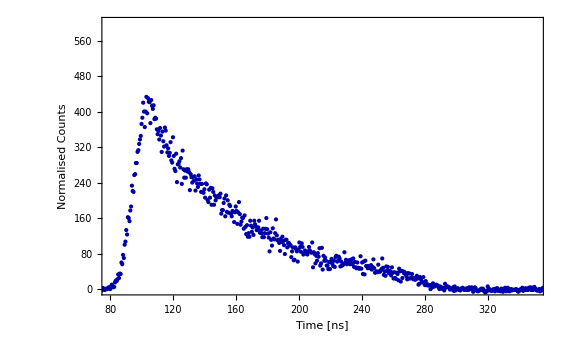

```mathematica
PicoBins=1;
BigBins493p1=Flatten[w={};Do[w={w,Total[NData493p1[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
BigBins493p2=Flatten[w={};Do[w={w,Total[NData493p2[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
TimeRange493=Range[(0)ns,(3583.6-0) ns,(512 ps*PicoBins)];
DataPhoton1=BigBins493p1-BigBins493p2;
DataPHOTON493p1=Transpose[{TimeRange493/ns,(DataPhoton1-Mean[Take[(DataPhoton1),{1,100}]])}];
PicoBins=1;
DataPlot=ListPlot[{DataPHOTON493p1},Axes->False,Frame->True,FrameLabel->{"Time [ns]","Normalised Counts"},Joined->False,PlotStyle->{{PointSize[Large],Darker[Blue]},{PointSize[Large],Red},{PointSize[Large],Green},{PointSize[Large],Lighter[Blue]},{PointSize[Large],Brown}},PlotRange->{{80,350},{-1,600}},FrameStyle->Directive[Thick,Black,40]]
```

```mathematica
CountsBkgSub=(DataPhoton1-Mean[Take[(DataPhoton1),{1,100}]]);
PhotonCounts=N[Total[Take[CountsBkgSub,{150,700}]]]
TotalReps=4*10^5*120;
PhotonProb=(PhotonCounts/TotalReps)*10^3
```

55178.1

1.14954

```mathematica
(*13th March tests*)
DataPico13thMarch=Import["G:\\Shared drives\\Ions\\03 - Projects\\Current Projects\\Rb Ba+ hybrid\\493 Photon Shape Tests\\14 Mar tests_2.dat",HeaderLines->10];
NData493p1=Flatten[DataPico13thMarch[[All,7]]];(*650 nm AOM pulsed at 200 ns - 5 uW*)
NData493p2=Flatten[DataPico13thMarch[[All,8]]];(*650 nm AOM pulsed at 200 ns - 5 uW background*)
```

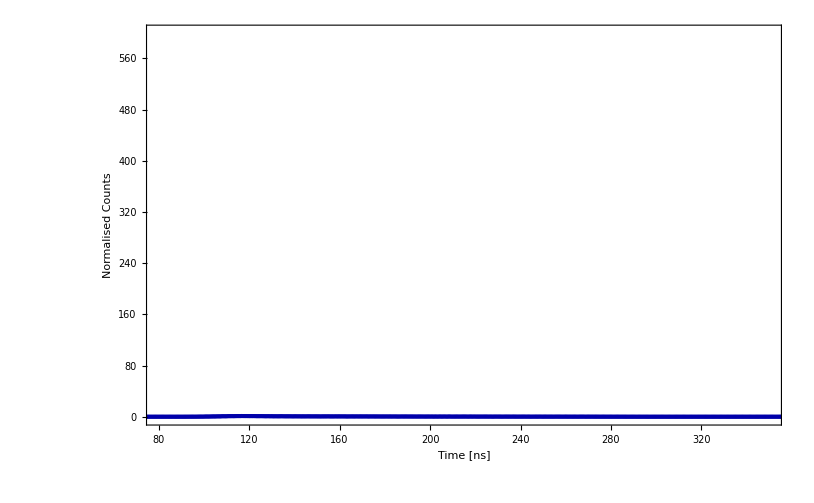

C:\Users\Ions\Desktop\GitHub\BaBlochCode

```mathematica
PicoBins=1;
BigBins493p1=Flatten[w={};Do[w={w,Total[NData493p1[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
BigBins493p2=Flatten[w={};Do[w={w,Total[NData493p2[[i;;i+(PicoBins-1)]]]},{i,1,7000,PicoBins}];w];
TimeRange493=Range[(0)ns,(3583.6-0) ns,(512 ps*PicoBins)];
DataPhoton1=BigBins493p1-BigBins493p2;
DataPHOTON493p1=Transpose[{TimeRange493/ns,(DataPhoton1-Mean[Take[(DataPhoton1),{1,100}]])/500}];
PicoBins=1;
DataPlot=ListPlot[{DataPHOTON493p1},Axes->False,Frame->True,FrameLabel->{"Time [ns]","Normalised Counts"},Joined->False,PlotStyle->{{PointSize[Large],Darker[Blue]},{PointSize[Large],Red},{PointSize[Large],Green},{PointSize[Large],Lighter[Blue]},{PointSize[Large],Brown}},PlotRange->{{80,350},{-1,600}},FrameStyle->Directive[Thick,Black,40]]
```

```mathematica
SetDirectory[NotebookDirectory[]]
time=Flatten[Import["_test_time.dat"]];
pop=Flatten[Import["_test_pop.dat"]];
pop2=Flatten[Import["_test_pop2.dat"]];
poptot=pop+pop2;
toff=95;
pulse1=Transpose[{time*1000+toff,pop/Max[pop]}];
pulse2=Transpose[{time*1000+toff,pop2/Max[pop+pop2]}];
pulsetot=Transpose[{time*1000+toff,(pop+pop2)/Max[pop]}];
ListPlot[{pulse1,pulse2,pulsetot,DataPHOTON493p1},PlotRange->{{50,500},All},Joined->True]
```

C:\Users\Ions\Desktop\GitHub\BaBlochCode

-Graphics-

```mathematica
Pulses={pulse1,pulse2,pulsetot};
```

```mathematica
Export["pulses.dat",{time,poptot,pop,pop2}]
```

pulses.dat

```mathematica
z=Import["pulses.dat"]
```

{1}
 |  |  |  |

```mathematica
z[[4]]
```

{0.,1.37243×10^-23,2.02563×10^-19,2.31896×10^-18,8.11642×10^-18,1.92716×10^-17,3.74611×10^-17,6.43617×10^-17,1.0165×10^-16,1.51002×10^-16,2.14096×10^-16,2.92607×10^-16,99976,0.000322065,0.000322046,0.000322027,0.000322007,0.000321988,0.000321969,0.00032195,0.000321931,0.000321912,0.000321893,0.000321873,0.000321854}
 |  |  |  |

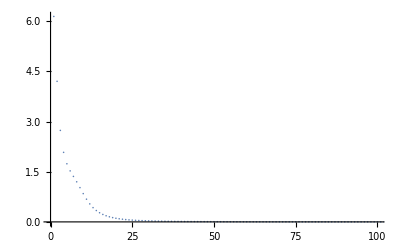

```mathematica
ListPlot[Abs[Chop[Fourier[pop]]],PlotRange->{{0,100},All}]
```

```mathematica
Fourier[pop]
```

{6.14632-6.592×10^-18 ⅈ,2.71791+3.20966 ⅈ,0.914446+2.57994 ⅈ,0.256052+2.06459 ⅈ,-0.125165+1.73448 ⅈ,99990,-0.424019-1.4661 ⅈ,-0.125165-1.73448 ⅈ,0.256052-2.06459 ⅈ,0.914446-2.57994 ⅈ,2.71791-3.20966 ⅈ}
 |  |  |  |